{5.508,5.508,5.508,5.508,5.50801,5.50801,5.50801,5.50802,5.50803,5.50804,5.50804,5.50805,5.50807,5.50808,5.50809,5.5081,5.50812,5.50814,5.50815,5.50817,5.50819,5.50821,5.50823,5.50825,5.50827,5.5083,5.50832,5.50835,5.50838,5.5084,5.50843,5.50846,5.50849,5.50852,5.50856,5.50859,5.50863,5.50866,5.5087,5.50874,29921,4.43729,4.43722,4.43716,4.43709,4.43703,4.43697,4.4369,4.43684,4.43677,4.43671,4.43665,4.43658,4.43652,4.43646,4.43639,4.43633,4.43626,4.4362,4.43614,4.43607,4.43601,4.43594,4.43588,4.43582,4.43575,4.43569,4.43563,4.43556,4.4355,4.43543,4.43537,4.43531,4.43524,4.43518,4.43511,4.43505,4.43499,4.43492,4.43486,4.43479}
 |  |  |  |

3.78965

0.

1.868

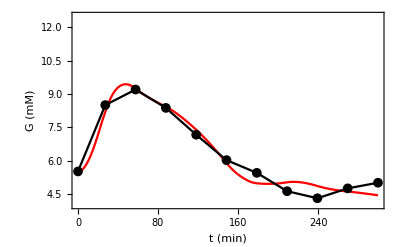

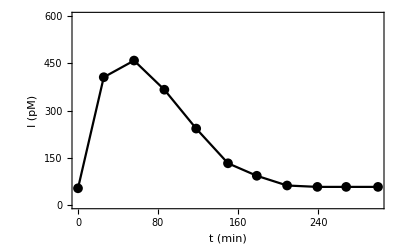

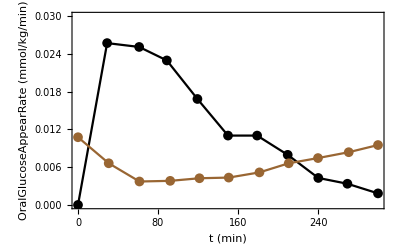

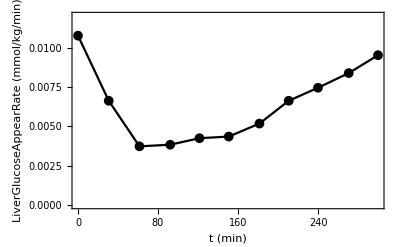

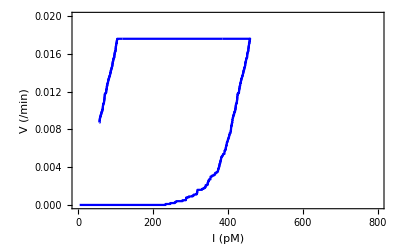

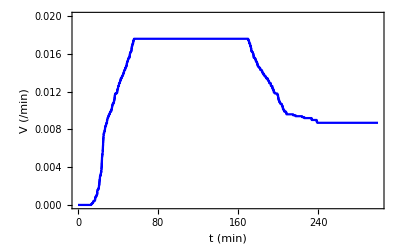

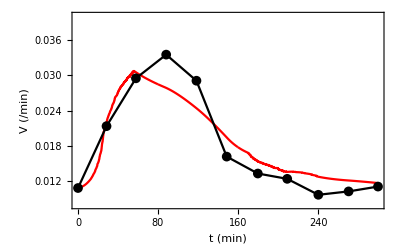

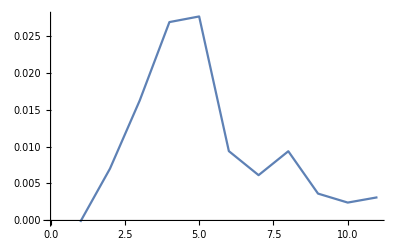

```mathematica
Remove["Global`*"];



h=0.01;

OralData=Flatten[Import[ToFileName[NotebookDirectory[],"iOral.txt"],"Data"]];
LiverData=Flatten[Import[ToFileName[NotebookDirectory[],"iLiver.txt"],"Data"]];
OraliverData=Flatten[Import[ToFileName[NotebookDirectory[],"iMeal.txt"],"Data"]];
s0=OraliverData[[1]];

BestParaBlock=Flatten[Import[ToFileName[NotebookDirectory[],"BestParaBlock.txt"],"Data"]];
Vsu=BestParaBlock[[4]];
Gsu=BestParaBlock[[5]];
Ome=BestParaBlock[[6]];


G=Flatten[Import[ToFileName[NotebookDirectory[],"G.txt"],"Data"]]
Len = Length[G];
Insulin=Flatten[Import[ToFileName[NotebookDirectory[],"I.txt"],"Data"]];

V=Flatten[Import[ToFileName[NotebookDirectory[],"V.txt"],"Data"]];


VofI = MapThread[List,{Insulin,V}];

V0=s0/Ome/G[[1]];

GGsu = G-Gsu;
GGsu = GGsu /. _?Negative -> 0;

VG = V G;

VGO= (VG+V0 G)  Ome + Vsu GGsu Ome;

TotalV0 = (Total[G]-0.5 G[[1]]-0.5 G[[Len]]) V0 Ome h

TotalVsu=Total[GGsu] Vsu Ome h

TotalVI=(Total[VG]-0.5 VG[[1]]-0.5 VG[[Len]])  Ome h

VGOData=Flatten[Import[ToFileName[NotebookDirectory[],"VGOData.txt"],"Data"]];
VGOTime=Flatten[Import[ToFileName[NotebookDirectory[],"VGOTime.txt"],"Data"]];
VGODataTime = MapThread[List,{VGOTime,VGOData}];




GData=Flatten[Import[ToFileName[NotebookDirectory[],"GData.txt"],"Data"]];
IData=Flatten[Import[ToFileName[NotebookDirectory[],"IData.txt"],"Data"]];
GTime=Flatten[Import[ToFileName[NotebookDirectory[],"GTime.txt"],"Data"]];
ITime=Flatten[Import[ToFileName[NotebookDirectory[],"ITime.txt"],"Data"]];
OralTime=Flatten[Import[ToFileName[NotebookDirectory[],"iOralTime.txt"],"Data"]];
LiverTime=Flatten[Import[ToFileName[NotebookDirectory[],"iLiverTime.txt"],"Data"]];
LenTime=Length[GTime];
GDataTime = MapThread[List,{GTime,GData}];
IDataTime = MapThread[List,{ITime,IData}];
OralDataTime=MapThread[List,{OralTime,OralData}];
LiverDataTime=MapThread[List,{LiverTime,LiverData}];




Show[
ListLinePlot[G,DataRange->{0,Len*h},PlotRange->{{0,300},{4,12.5}},Frame->True,FrameLabel->{"t (min)","G (mM)"},LabelStyle->20,FrameTicksStyle->Directive[18],PlotStyle->Red],
ListLinePlot[GDataTime,PlotMarkers->{Automatic, 10},PlotStyle->Black]
]

Export[ToFileName[NotebookDirectory[],"GData.eps"],%];

(*
Show[
ListLinePlot[Insulin,DataRange->{0,Len*h},PlotRange->{{0,300},{0,600}},Frame->True,FrameLabel->{"t (min)","I (pM)"},LabelStyle->20,FrameTicksStyle->Directive[18],PlotStyle->Red],
ListPlot[IDataTime,PlotMarkers->{Automatic, 10},PlotStyle->Red]
]
*)

ListLinePlot[IDataTime,PlotMarkers->{Automatic, 10},PlotStyle->Black,PlotRange->{{0,300},{0,600}},Frame->True,FrameLabel->{"t (min)","I (pM)"},LabelStyle->20,FrameTicksStyle->Directive[18]]

Export[ToFileName[NotebookDirectory[],"IData.eps"],%];

Show[
ListLinePlot[OralDataTime,PlotMarkers->{Automatic,10},PlotStyle->Black,PlotRange->{{0,300},{0,0.030}},Frame->True,FrameLabel->{"t (min)","OralGlucoseAppearRate (mmol/kg/min)"},LabelStyle->15,FrameTicksStyle->Directive[14]],
ListLinePlot[LiverDataTime,PlotMarkers->{Automatic,10},PlotStyle->Brown]
]
Export[ToFileName[NotebookDirectory[],"Oral.eps"],%];


ListLinePlot[LiverDataTime,PlotMarkers->{Automatic,10},PlotStyle->Black,PlotRange->{{0,300},{0,0.012}},Frame->True,FrameLabel->{"t (min)","LiverGlucoseAppearRate (mmol/kg/min)"},LabelStyle->15,FrameTicksStyle->Directive[18]]

Export[ToFileName[NotebookDirectory[],"Liver.eps"],%];

ListLinePlot[VofI,PlotRange->{{0,800},{0,0.02}},Frame->True,FrameLabel->{"I (pM)","V (/min)"},LabelStyle->20,FrameTicksStyle->Directive[18],PlotStyle->Blue]


Export[ToFileName[NotebookDirectory[],"VI.eps"],%];

ListLinePlot[V,DataRange->{0,Len*h},PlotRange->{{0,300},{0,0.02}},Frame->True,FrameLabel->{"t (min)","V (/min)"},LabelStyle->20,FrameTicksStyle->Directive[18],PlotStyle->Blue]

Show[
ListLinePlot[VGO,DataRange->{0,Len*h},PlotRange->{{0,300},{0.008,0.04}},Frame->True,FrameLabel->{"t (min)","V (/min)"},LabelStyle->20,FrameTicksStyle->Directive[18],PlotStyle->Red],
ListLinePlot[VGODataTime,PlotMarkers->{Automatic, 10},PlotStyle->Black]
]

Export[ToFileName[NotebookDirectory[],"VGO.eps"],%];

ListLinePlot[VGOData/GData/0.075-ConstantArray[V0,Length[VGOData]]]
```